The following code is part of Natasha Dada’s Wolfram Summer School 2018 project, An Analysis of Word Choice in the Real Estate Industry. This code performs a Term Frequency - Inverse Document Frequency (TF-IDF) analysis on a collection of MLS house listings from the Boston area from April-June 2018.

A list of house listings, each in the form {house description (string), percent difference between listing and selling price of the house (number)}:

```mathematica
data = Get["data.mx"];
```

A list of the house descriptions:

```mathematica
corpus = data[[All,1]];
```

The corpus stemmed without stopwords or numerical values:

```mathematica
tokenizedCorpus = Select[WordStem@TextWords@ToLowerCase@DeleteStopwords@#,!StringContainsQ[#,{"0","1","2","3","4","5","6","7","8","9"}]&]&/@corpus;
```

A neural net from the Wolfram Neural Net Repository for feature extraction of words:

```mathematica
glove=
NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"];
```

Functions to determine term frequency and inverse document frequency of each word. The product of these two results is a word’s TF-IDF score:

```mathematica
tf[word_String, tokenizedText_] := N[Count[tokenizedText,word] / Length[tokenizedText]]

idf[word_, tokenizedCorpus_] := N @ Log[ 10, Length[tokenizedCorpus] / Count[tokenizedCorpus, l_List /; MemberQ[l ,word]] ]
```

A list of associations, one for each listing, in which each word in a listing is associated with its TF-IDF score:

```mathematica
(*wordScores=Table[AssociationMap[tf[#,tokenizedCorpus[[n]]]*idf[#,tokenizedCorpus]&,DeleteDuplicates@tokenizedCorpus[[n]]],{n,Length[tokenizedCorpus]}];*)
```

```mathematica
(*Put[wordScores,"wordScores.mx"];*)
```

```mathematica
wordScores=Get["wordScores.mx"];
```

The top five words, based of TF-IDF score, of each listing:

```mathematica
wordScoresTopFive = Take[Sort[#,Greater],5]&/@wordScores;
```

A list of top words from every listing in the form {word, score of listing} with the scores of duplicate words averaged:

```mathematica
allTopWords= 
Flatten[Table[{#,Last[data[[n]]]}&/@Keys[wordScoresTopFive[[n]]],{n,Length[wordScoresTopFive]}],1]; allTopWords = SortBy[{First[First[#]],Mean[Last/@#]}&/@GatherBy[allTopWords,First],Last];
```

A list of words whose listing has a negative score:

```mathematica
negativeWords=Select[allTopWords,Last[#]<0&];
```

Negative scores rescaled between 0 and 0.5 which will correspond to different shades of red:

```mathematica
rescaledNegativeScores = Rescale[negativeWords[[All,2]],MinMax[negativeWords[[All,2]]],{0,0.5}];
```

A list of words whose listing has a score of 0:

```mathematica
neutralWords=Select[allTopWords,Last[#]==0&];
```

Words with neural scores assigned a score of 0.5 which will correspond to a mix of red and green:

```mathematica
rescaledNeutralScores = Table[0.5,Length[neutralWords]];
```

A list of words whose listing has a positive score:

```mathematica
positiveWords=Select[allTopWords,Last[#]>0&];
```

Positive scores rescaled between 0.5 and 1 which will correspond to different shades of green:

```mathematica
rescaledPositiveScores = Rescale[positiveWords[[All,2]],MinMax[positiveWords[[All,2]]],{0.5,1}];
```

The scores of all top words rescaled to values between 0 and 1:

```mathematica
rescaledScores = Join[rescaledNegativeScores,rescaledNeutralScores,rescaledPositiveScores];
```

A list of each top word in the form {word, rescaled score}:

```mathematica
rescaledWords = Transpose[{allTopWords[[All,1]],rescaledScores}];
```

A feature space plot that used a neural net to map each word. The color of each word corresponds to its success:

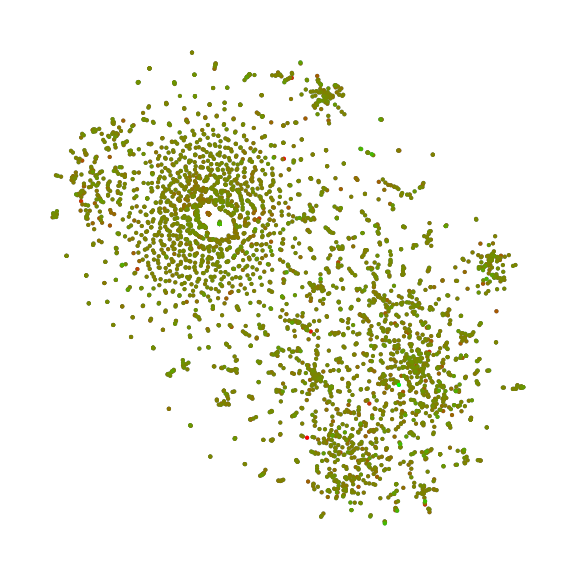

```mathematica
FeatureSpacePlot[Style[First[#],RGBColor[1-Last[#],Last[#],0]]&/@rescaledWords,FeatureExtractor->glove,LabelingFunction->Tooltip,ImageSize->Large,PlotStyle->Directive[PointSize[Medium]]]
```

The ranks of all top words, from lowest to highest TF-IDF score, scaled from 0 to 1:

```mathematica
ranks = Rescale[Range[Length[allTopWords]],MinMax[Range[Length[allTopWords]]],{0,1}];
```

A list of each top word in the form {word, rank}:

```mathematica
rankedWords=Transpose[{allTopWords[[All,1]],ranks}];
```

A feature space plot that used a neural net to map each word. The color of each word corresponds to its success:

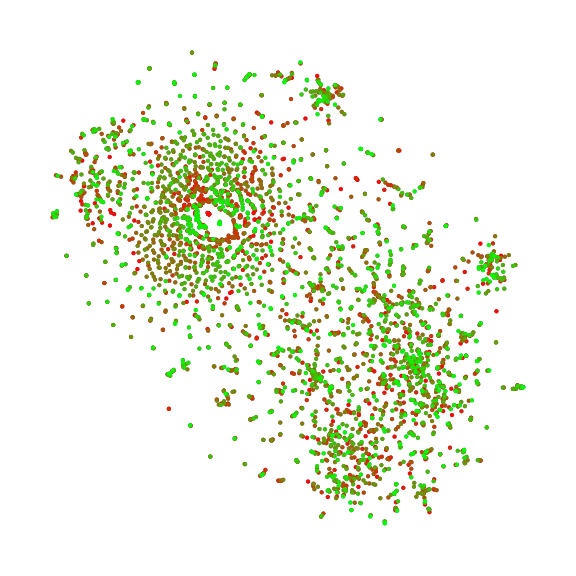

```mathematica
FeatureSpacePlot[Style[First[#],RGBColor[1-Last[#],Last[#],0]]&/@rankedWords,FeatureExtractor->glove,LabelingFunction->Tooltip,ImageSize->Large,PlotStyle->Directive[PointSize[Medium]]]
```